## Init

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
ClearAll["Global`*"]
Needs["NumericalCalculus`"]
$Assumptions={_∈Reals,-Pi<θ<Pi &&-Pi<ϕ<Pi && -Pi<φ<Pi && -Pi<δ<Pi && c > 0 && ω >0 && w0>0 && z >=0 && h >0 && E0 > 0 && r >0 && l∈Reals && x∈Reals && y ∈Reals &&t>0 && β∈Reals && α∈Reals && γ∈Reals,Tp>0,T>0,a0>0,a00>0}
rule2carte ={r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
rule2pol = {x->r Cos[θ],y-> r Sin[θ]};
k := ω/c
zR:=1/2*k*w0^2 (*Rayleigh range*)
w[z] := w0 *Sqrt[1+(z/zR)^2] (* Beam radius *)
R[z] := z*(1+(zR/z)^2) (* Radius of curvature *)
p:=0
n := Abs[l]+2*p
G[z]:= (n+1)ArcTan[z/zR](* Gouy phase at z *)
Gpl := Sqrt[(2*Factorial[p])/(Pi*Factorial[p+Abs[l]])]*0+1
Lp := 1(* generalized Laguerre polynomials p = 0 -> Lp = 1 *)
If[p ==1,Lp = 1 +Abs[l]-(2*r^2)/w[z]^2;]
f[r]=(w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2];
u[r,θ,z]:=Evaluate[f[r]*Lp*Exp[-I k r^2/(2 R[z])]*Exp[-I*l*θ]*Exp[I*G[z]]];(*((2r^2)/w[z]^2)*)

Ex[r,θ,z]=E0*u[r,θ,z]*Exp[-I*k*z+I*ω*t]; (**tempEnv*)
Ey[r,θ,z]=0;
Ez[r,θ,z]=0;

Ex[x,y,z] =Ex[r,θ,z]/. {r->Norm[{x,y}],θ->ArcTan[x,y]};

Clear[l]
l=1;
c = 1;
ω = 1;
φ=0;
Ev = Evaluate[{Ex[x,y,z],0,0}]/.{Abs[x]->RealAbs[x],Abs[y]->RealAbs[y]}//Simplify
EzO3=Evaluate[-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](√2 ⅇ^(-1/2 ⅈ ((2 α^2)/(ⅈ+γ)+(2 β^2)/(ⅈ+γ)-2 (φ+t ω)-4 ArcTan[γ])) E0 (ⅈ-2 ⅈ α^2-2 α β+γ) ω)/(c h (-ⅈ+γ) (ⅈ+γ)^2)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}]; (*L=1*)
EzO5=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2 ⅈ √2 ⅇ^(-(ⅈ (2 α^2+2 β^2+(ⅈ+γ) (-2 (φ+t ω))))/(2 (ⅈ+γ))) E0 (-2 α^4+2 ⅈ α^3 β+2 ⅈ α β (-3+β^2+3 ⅈ γ)+α^2 (7-2 β^2-7 ⅈ γ)+(ⅈ+γ) (2 ⅈ-ⅈ β^2+2 γ)) ω)/(c h^3 (ⅈ+γ)^5)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}(*L=l*);
EzLGO3 = EzO3 ;
EzLGO5 = EzO3 +EzO5;
Evn2 = {Ex[x,y,z],0, EzLGO5}//Simplify;
Bn2 = I/ω *Evn2{x,y,z}//Simplify;
```

{_∈ℝ,-π<θ<π&&-π<ϕ<π&&-π<φ<π&&-π<δ<π&&c>0&&ω>0&&w0>0&&z≥0&&h>0&&E0>0&&r>0&&l∈ℝ&&x∈ℝ&&y∈ℝ&&t>0&&β∈ℝ&&α∈ℝ&&γ∈ℝ,Tp>0,T>0,a0>0,a00>0}

{(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2))/(w0^4+4 z^2),0,0}

```mathematica
(*Fields with time envelope*)
```

```mathematica
cGauss = Sqrt[Pi/2]
gaussEnv = Exp[-((t-z-1.25*Tp)/(Tp*3/8/cGauss))^2];
EzN[x_,y_,z_,t_] = EzLGO5*gaussEnv//Simplify
AzN[x_,y_,z_,t_] = Integrate[EzLGO5*gaussEnv,t]//Simplify


Et=Re[Evn2]*gaussEnv/.h->w0;
Bt=Re[Bn2]*gaussEnv/.h->w0;
gam=Sqrt[1+px[t]^2+py[t]^2+pz[t]^2];
```

√(π/2)

(√2 ⅇ^(-(17.4533 (0.8 t-1. Tp-0.8 z)^2)/Tp^2-(-ⅈ t w0^2+x^2+y^2-2 t z+ⅈ w0^2 z+2 z^2)/(w0^2-2 ⅈ z)) E0 (4 x^4-4 ⅈ x^3 y-2 x^2 (7 w0^2-2 (y^2+7 ⅈ z))+(ⅇ^(2 ⅈ ArcTan[(2 z)/w0^2]) (w0^2-2 ⅈ z)^3 (w0^2-2 x^2+2 ⅈ x y-2 ⅈ z))/(w0^2+2 ⅈ z)+2 (w0^2-2 ⅈ z) (2 w0^2-y^2-4 ⅈ z)+4 x y (3 ⅈ w0^2-ⅈ y^2+6 z)))/(w0^7 (ⅈ+(2 z)/w0^2)^5)

1/(w0^7 (ⅈ+(2 z)/w0^2)^5)(0.+0.375 ⅈ) ⅇ^((Tp^2 ((3.55271×10^-15+0. ⅈ) w0^4+w0^2 ((-1.+0. ⅈ) x^2-(1.+0. ⅈ) y^2-(0.+1.42109×10^-14 ⅈ) z)+((0.+2. ⅈ) x^2+(0.+2. ⅈ) y^2-(1.42109×10^-14+0. ⅈ) z) z)+Tp z ((3.55271×10^-15+0. ⅈ) w0^4-(0.+1.42109×10^-14 ⅈ) w0^2 z-(1.42109×10^-14+0. ⅈ) z^2)+z^2 ((1.77636×10^-15+0. ⅈ) w0^4-(0.+7.10543×10^-15 ⅈ) w0^2 z-(7.10543×10^-15+0. ⅈ) z^2)+Tp^3 ((0.+1.25 ⅈ) w0^4+(5.+0. ⅈ) w0^2 z-(0.+5. ⅈ) z^2)+Tp^4 ((-0.0223812+0. ⅈ) w0^4+(0.+0.0895247 ⅈ) w0^2 z+(0.0895247+0. ⅈ) z^2))/(Tp^2 ((1.+0. ⅈ) w0^2-(0.+2. ⅈ) z)^2)) E0 Tp (4 x^4-4 ⅈ x^3 y-2 x^2 (7 w0^2-2 (y^2+7 ⅈ z))+(ⅇ^(2 ⅈ ArcTan[(2 z)/w0^2]) (w0^2-2 ⅈ z)^3 (w0^2-2 x^2+2 ⅈ x y-2 ⅈ z))/(w0^2+2 ⅈ z)+2 (w0^2-2 ⅈ z) (2 w0^2-y^2-4 ⅈ z)+4 x y (3 ⅈ w0^2-ⅈ y^2+6 z)) Erfi[(3.34217 t w0^2-4.17771 Tp w0^2-(0.+0.149603 ⅈ) Tp^2 w0^2-(0.+6.68434 ⅈ) t z+(0.+8.35543 ⅈ) Tp z-0.299207 Tp^2 z-3.34217 w0^2 z+(0.+6.68434 ⅈ) z^2)/((0.+1. ⅈ) Tp w0^2+2. Tp z)]

```mathematica
Re[EzLGO5]*gaussEnv//Simplify
```

-(2 √2 ⅇ^(-(17.4533 (0.8 t-1. Tp-0.8 z)^2)/Tp^2-(-ⅈ t w0^2+x^2+y^2-2 t z+ⅈ w0^2 z+2 z^2)/(w0^2-2 ⅈ z)) E0 w0^3 (2 w0^4-w0^2 (7 x^2-6 ⅈ x y+y^2+8 ⅈ z)+2 (x^4-ⅈ x^3 y+x^2 (y^2+7 ⅈ z)+ⅈ (y^2+4 ⅈ z) z+x (-ⅈ y^3+6 y z))))/((-ⅈ w0^2-2 z)^5)

```mathematica
IntEzLGO5 = ComplexExpand[EzLGO5*Conjugate[EzLGO5]]*(gaussEnv)^2/.h->w0//Simplify;
IntEx=((E0*w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2]*gaussEnv)^2/.h->w0;
```

```mathematica
(**)
```

```mathematica
(*Equation of motion*)
```

```mathematica
eq0={D[px[t],t],D[py[t],t],D[pz[t],t]}-ee*(Et+Cross[{px[t],py[t],pz[t]},Bt]/gam)/.{x->x[t],y->y[t],z->z[t]};
```

```mathematica
(*Function, which solves equation of motion*)
```

```mathematica
sol[a00_,w00_,T0_,x0_,y0_,z0_,dt_,tmax_,ee0_]:=NDSolve[{(eq0=={0,0,0})/.{E0->a00,T->T0,w0->w00,ee->ee0},D[y[t],t]==py[t]/gam,D[z[t],t]==pz[t]/gam,D[x[t],t]==px[t]/gam,px[-20]==0,py[-20]==0,pz[-20]==0,x[-20]==x0,y[-20]==y0,z[-20]==z0},{px,py,pz,x,y,z},{t,-20,tmax},StartingStepSize->dt,PrecisionGoal->20]
```

```mathematica
(*Calculation of Mz for 4 particles starting at (1,1), (-1,1), (-1,-1) and (1,-1)*)
```

```mathematica
MzDistrib[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,mz},
soll=sol[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax]
```

## Ax & Ex To Python

```mathematica
gaussEnv
```

ⅇ^(-(32 π (t-1.25 Tp-z)^2)/(9 Tp^2))

```mathematica
Integrate[gaussEnv,t]
```

0.265165 Tp Erf[(4.17771 (0.8 t-1. Tp-0.8 z))/Tp]

```mathematica
EzFirstSimple = (ComplexExpand[Re[EzLGO5]/.rule2pol//Simplify]/.{(w0^4 (t-z))/(w0^4+4 z^2)+(2 z (-r^2+2 (t-z) z))/(w0^4+4 z^2)->ϕ})/.{ⅇ^(-(r^2 w0^2)/(w0^4+4 z^2)) E0->Ω};
EzPy[x_,y_,z_,t_]=FullSimplify[Re[EzFirstSimple]]*gaussEnv
```

1/((w0^4+4 z^2)^5)2 √2 ⅇ^(-(32 π (t-1.25 Tp-z)^2)/(9 Tp^2)) w0^3 Ω (2 r^2 z (-12 w0^2 (w0^8-16 z^4)+r^2 (5 w0^8-40 w0^4 z^2+16 z^4)) Cos[2 θ-ϕ]+2 z (2 (3 w0^4-4 z^2) (w0^4+4 z^2)^2-16 r^2 w0^2 (w0^8-16 z^4)+r^4 (5 w0^8-40 w0^4 z^2+16 z^4)) Cos[ϕ]-r^2 (r^2 w0^2 (w0^8-40 w0^4 z^2+80 z^4)-3 (w0^12-20 w0^8 z^2-80 w0^4 z^4+64 z^6)) Sin[2 θ-ϕ]+(2 (w0^4-12 z^2) (w0^5+4 w0 z^2)^2+r^4 w0^2 (w0^8-40 w0^4 z^2+80 z^4)-4 r^2 (w0^12-20 w0^8 z^2-80 w0^4 z^4+64 z^6)) Sin[ϕ])

```mathematica
gaussEnvPy = Exp[-((t-z-tCenter)/(Tp/sigma))^2];
AzFirstSimple = (((ComplexExpand[Integrate[Re[EzLGO5]*gaussEnvPy//Simplify,t]])/.{-Tp^2/(4 sigma^2)-(w0^2 x^2)/(w0^4+4 z^2)-(w0^2 y^2)/(w0^4+4 z^2)->κ})/.{Tp/(2 sigma)-(ⅈ sigma (-t+tCenter+z))/Tp->ψ})/.{(tCenter w0^4)/(w0^4+4 z^2)-(2 z (x^2+y^2-2 tCenter z))/(w0^4+4 z^2)->ξ};
AzPy[x_,y_,z_,t_]=FullSimplify[Re[AzFirstSimple]]
```

1/(sigma (w0^4+4 z^2)^5)ⅇ^κ E0 √(2 π) Tp w0^3 Erfi[ψ] ((-2 w0^14+w0^12 (7 x^2+y^2)-20 w0^8 z (x^3 y+x y^3+7 x^2 z+y^2 z)-80 w0^4 z^3 (-2 x y (x^2+y^2)+(7 x^2+y^2) z)+64 z^5 (-x y (x^2+y^2)+(7 x^2+y^2) z)-32 w0^2 z^4 (5 x^2 (x^2+y^2)+24 x y z-12 z^2)-2 w0^10 (x^4+x^2 y^2-24 x y z-4 z^2)+80 w0^6 z^2 (x^4+x^2 y^2+2 z^2)) Cos[ξ]+2 (40 w0^6 x y (x^2+y^2) z^2+3 w0^12 (x y+2 z)+16 w0^2 z^4 (-5 x y (x^2+y^2)+4 (7 x^2+y^2) z)-w0^10 (x y (x^2+y^2)+4 (7 x^2+y^2) z)+32 z^5 (x^4+x^2 y^2+6 x y z-4 z^2)-16 w0^4 z^3 (5 x^2 (x^2+y^2)+15 x y z-2 z^2)+10 w0^8 z (x^4+x^2 y^2-6 x y z+4 z^2)) Sin[ξ])

```mathematica
(EzPy[r0Traj,theta0Traj,z0Traj,t]/.{ϕ->(w0^4 (t-z))/(w0^4+4 z^2)+(2 z (-r^2+2 (t-z) z))/(w0^4+4 z^2),Ω->ⅇ^(-(r^2 w0^2)/(w0^4+4 z^2)) E0})/.{z->z0Traj,r->r0Traj,θ->theta0Traj}
```

1.91471×10^-20 ⅇ^(-1.20205-(-125.664+t)^2/(162 π)) (1.24663×10^16 Cos[0.939103 (-10 π+t)+0.000969201 (-32 π^2+20 π (-10 π+t))]-1.66716×10^17 Sin[0.939103 (-10 π+t)+0.000969201 (-32 π^2+20 π (-10 π+t))])

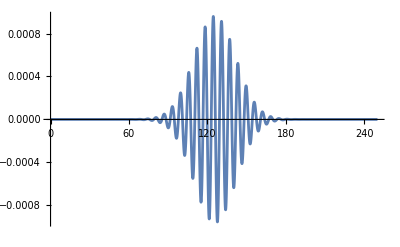

```mathematica
Plot[(EzPy[r0Traj,theta0Traj,z0Traj,t]/.{ϕ->(w0^4 (t-z))/(w0^4+4 z^2)+(2 z (-r^2+2 (t-z) z))/(w0^4+4 z^2),Ω->ⅇ^(-(r^2 w0^2)/(w0^4+4 z^2)) E0})/.{z->z0Traj,r->r0Traj,θ->theta0Traj},{t,0,250},PlotRange->All]
```

## Numerical

```mathematica
l0=2Pi;
tmax = 60*l0;
dt = 0.000001;
w0=2.5*l0;
a0=2.0;
E0=a0;
z0=5*l0;
Tp=12*l0;
```

```mathematica
gaussEnv/.{T->Tp}
```

ⅇ^(-(-94.2478+t-z)^2/(162 π))

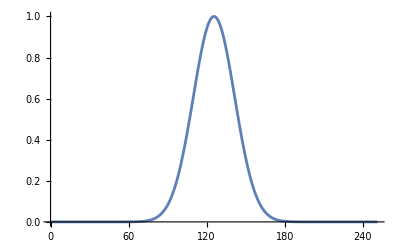

```mathematica
Plot[gaussEnv/.{T->Tp,z->z0},{t,0,40*l0}]
```

### Longitudinal Momentum & Displacement

```mathematica
x0Traj=2*l0;
y0Traj=2*l0;
z0Traj = 5*l0;
r0Traj = Sqrt[x0Traj^2+y0Traj^2];
theta0Traj = ArcTan[x0Traj,y0Traj];
```

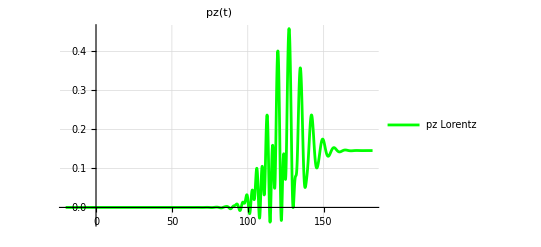

```mathematica
soll=sol[a0,w0,Tp,x0Traj,y0Traj,z0Traj,dt,Tp*2+z0Traj,-1];
pzSol[t_]=(pz[t]/.soll);
Plot[{pzSol[t]},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"pz Lorentz"},PlotLabel->"pz(t)"]
```

## Compare Ez vs Az vs pz

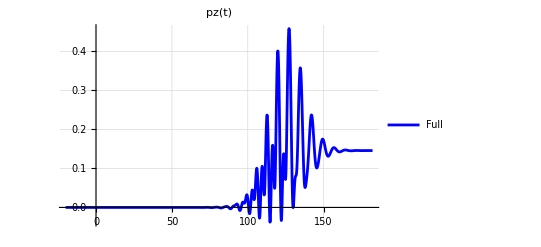

```mathematica
Plot[{pzSol[t]},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue},PlotLegends->{"Full"},PlotLabel->"pz(t)"]
```

```mathematica
EzN[x0Traj,y0Traj,z0Traj,5]
```

1.69021×10^-14-1.07454×10^-14 ⅈ

```mathematica
EzN[0,0,z0Traj,t]
```

(0.0826834-0.15045 ⅈ) ⅇ^(-0.00307012 (-100.531+0.8 t)^2-(0.00380604+0.000969201 ⅈ) ((1973.92+7751.57 ⅈ)-(0.+246.74 ⅈ) t-20 π t))

```mathematica
EzN[x,y,z,t]
```

(1.19869×10^-8 ⅇ^(-0.00307012 (-75.3982+0.8 t-0.8 z)^2-((0.-246.74 ⅈ) t+x^2+y^2+(0.+246.74 ⅈ) z-2 t z+2 z^2)/(246.74-2 ⅈ z)) (4 x^4-4 ⅈ x^3 y-2 x^2 (1727.18-2 (y^2+7 ⅈ z))+(ⅇ^(2 ⅈ ArcTan[0.00810569 z]) (246.74-2 ⅈ z)^3 (246.74-2 x^2+2 ⅈ x y-2 ⅈ z))/(246.74+2 ⅈ z)+2 (246.74-2 ⅈ z) (493.48-y^2-4 ⅈ z)+4 x y ((0.+740.22 ⅈ)-ⅈ y^2+6 z)))/(ⅈ+0.00810569 z)^5

```mathematica
Re[EzN[0,0,0,t]]
```

Re[(0.-0.182982 ⅈ) ⅇ^(-0.00405285 ((0.+0. ⅈ)-(0.+246.74 ⅈ) t)-0.00307012 (-75.3982+0.8 t)^2)]

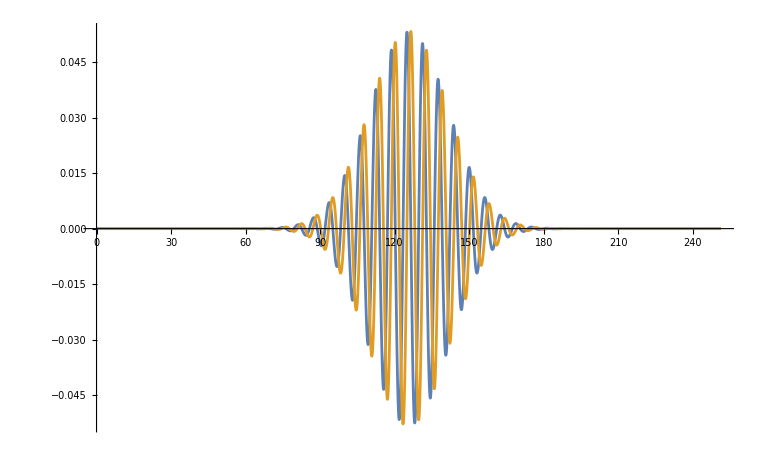

```mathematica
Plot[{Re[EzN[x0Traj,y0Traj,z0Traj,t]],Re[AzN[x0Traj,y0Traj,z0Traj,t]],EzPy[x0Traj,y0Traj,z0Traj,t]},{t,0,40*l0},PlotRange->All]
```

3.17178×10^-30 ⅇ^((0.987654-0.00392975 t) t)

(0.-3.46112×10^-111 ⅈ) Erf[(5.57029+11.2798 ⅈ)-0.0443269 t] Erfi[(11.2798+5.57029 ⅈ)-(0.+0.0443269 ⅈ) t]

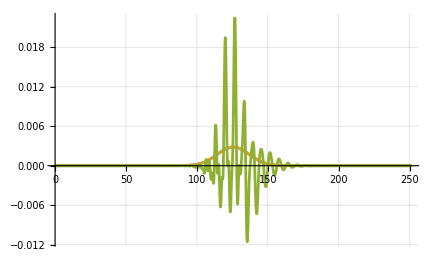

```mathematica
EzN2 = EzN[x0Traj,y0Traj,z0Traj,t]*Conjugate[EzN[x0Traj,y0Traj,z0Traj,t]]//FullSimplify
AzN2 =AzN[x0Traj,y0Traj,z0Traj,t]*Conjugate[AzN[x0Traj,y0Traj,z0Traj,t]]//FullSimplify
Plot[{Re[EzN2],Re[AzN2],Re[AzN[x0Traj,y0Traj,z0Traj,t]]*pzSol[t]},{t,0,40*l0},PlotRange->All,GridLines->Automatic]
```

```mathematica
IntEz = NIntegrate[EzN2,{t,0,250}];
IntAz = NIntegrate[AzN2,{t,0,250}];
IntAzPz = NIntegrate[Re[AzN[x0Traj,y0Traj,z0Traj,t]]*pzSol[t],{t,0,250}][[1]];
IntEzPz = NIntegrate[Re[EzN[x0Traj,y0Traj,z0Traj,t]]*pzSol[t],{t,0,250}][[1]];
Print["Ez^2 = ",IntEz]
Print["Az^2 = ",IntAz]
Print["Ez*pz = ",IntEzPz]
Print["Az*pz = ",IntAzPz]
```

Ez^2 = 0.0800459

Az^2 = 0.0805224

Ez*pz = -0.0198904

Az*pz = 0.0356218

```mathematica
Integrate[EzN[x0Traj,y0Traj,z0Traj,t]*Conjugate[EzN[x0Traj,y0Traj,z0Traj,t]]//FullSimplify,{t,-Infinity,Infinity}]
Integrate[Re[AzN[x0Traj,y0Traj,z0Traj,t]*Conjugate[AzN[x0Traj,y0Traj,z0Traj,t]]]//FullSimplify,{t,0,250}]
```

0.0800459-1.21665×10^-15 ⅈ

0.

```mathematica
EzN[x0Traj,y0Traj,z0Traj,t]*Conjugate[EzN[x0Traj,y0Traj,z0Traj,t]]//Simplify
```

3.17178×10^-30 ⅇ^((0.987654-0.00392975 t) t)